```mathematica
fonstat[lmax_, cnorm_, IC50_,s_, r_, d_]:=s*IC50*cnorm*lmax/(1+cnorm^4)/((1-r)*lmax/(1+cnorm^4)+(1-s*IC50*cnorm)*d)
```

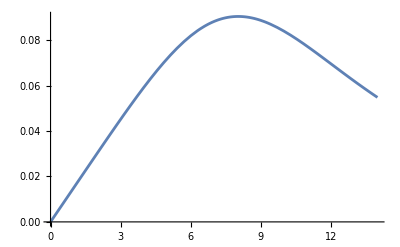

```mathematica
Plot[fonstat[1.7, x/4.9, 4.9,0.016,0, 0.1], {x,0,14}]
```

```mathematica
D[fonstat[lmax, cnorm, IC50, s, r, d], cnorm]
```

-(cnorm IC50 lmax s (-(4 cnorm^3 lmax (1-r))/((1+cnorm^4)^2)-d IC50 s))/((1+cnorm^4) ((lmax (1-r))/(1+cnorm^4)+d (1-cnorm IC50 s))^2)-(4 cnorm^4 IC50 lmax s)/((1+cnorm^4)^2 ((lmax (1-r))/(1+cnorm^4)+d (1-cnorm IC50 s)))+(IC50 lmax s)/((1+cnorm^4) ((lmax (1-r))/(1+cnorm^4)+d (1-cnorm IC50 s)))

```mathematica
Simplify[%23]
```

(IC50 lmax s (d-3 cnorm^4 d+lmax-lmax r+4 cnorm^5 d IC50 s))/((lmax (-1+r)+(1+cnorm^4) d (-1+cnorm IC50 s))^2)

```mathematica
foncidal[lmax_, cnorm_, IC50_,s_, r_, d_]:= s*IC50*cnorm*lmax/(lmax*(s*IC50*cnorm-r)+d+lmax/(1+cnorm^4))
```

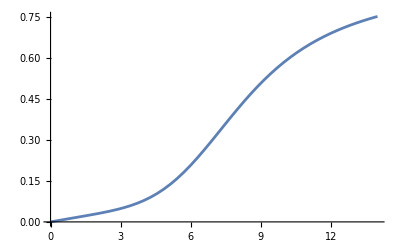

```mathematica
Plot[foncidal[1.7, x/4.9, 4.9,0.016,0, 0.1], {x,0,14}]
```

```mathematica
D[foncidal[lmax, cnorm, IC50,s, r, d], cnorm]
```

-(cnorm IC50 lmax s (-(4 cnorm^3 lmax)/((1+cnorm^4)^2)+IC50 lmax s))/((d+lmax/(1+cnorm^4)+lmax (-r+cnorm IC50 s))^2)+(IC50 lmax s)/(d+lmax/(1+cnorm^4)+lmax (-r+cnorm IC50 s))

```mathematica
Simplify[-(cnorm IC50 lmax s (-(4 cnorm^3 lmax)/((1+cnorm^4)^2)+IC50 lmax s))/((d+lmax/(1+cnorm^4)+lmax (-r+cnorm IC50 s))^2)+(IC50 lmax s)/(d+lmax/(1+cnorm^4)+lmax (-r+cnorm IC50 s))]
```

-(IC50 lmax (-(1+cnorm^4)^2 d+lmax (-1+r+cnorm^8 r+cnorm^4 (-5+2 r))) s)/(((1+cnorm^4) d+lmax (1-(1+cnorm^4) r+cnorm IC50 s+cnorm^5 IC50 s))^2)